### Ejemplos de código

```mathematica
sol=DSolveValue[y'[x]+y[x]==x,y[x],x]
```

-1+x+ⅇ^-x C[1]

```mathematica
DSolveValue[{y'[x]+y[x]==x,y[0]==-1},y[x],x]
```

-1+x

```mathematica
NDSolveValue[{y'[x]==Cos[x^2],y[0]==0},y[x],{x,-5,5}]
```

InterpolatingFunction[…][x]

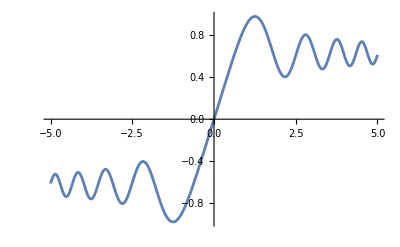

```mathematica
Plot[%,{x,-5,5}]
```

```mathematica
{xsol,ysol}=NDSolveValue[{x'[t]==-y[t]-x[t]^2,y'[t]==2 x[t]-y[t]^3,x[0]==y[0]==1},{x,y},{t,20}]
```

{InterpolatingFunction[…],InterpolatingFunction[…]}

InterpolatingFunction::dmval: Input value {-39.9984} lies outside the range of data in the interpolating function. Extrapolation will be used.

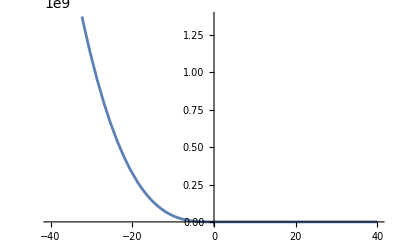

```mathematica
Plot[xsol[t], {t, -40, 40}]
```

## Dependencia Lineal Δ(t) = β^2t , Ω = 0

```mathematica
H1 =MatrixForm[{{β^2 t, Ω}, {Ω, - β^2 t}}]
```

(t β^2 | Ω
Ω | -t β^2)

```mathematica
Eigenvalues[%]
```

{-√(t^2 β^4+Ω^2),√(t^2 β^4+Ω^2)}

```mathematica
Eigenvectors[%]
```

Eigenvectors[{-√(t^2 β^4+Ω^2),√(t^2 β^4+Ω^2)}]

```mathematica
Manipulate[Plot[{(β^2)t,-(β^2)t,√(t^2 β^4+Ω^2),-√(t^2 β^4+Ω^2)},{t,-40.1,40.1},
PlotRange->{-6,6},Frame->True,Axes->False,
FrameLabel->{Style["Time",25,FontFamily->"Times New Roman",Black],
Style["Energy",25,FontFamily->"Times New Roman",Black]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,
PlotStyle->{Directive[Green,Dashed,Thick],
Directive[Purple,Dashed,Thick],
Directive[Red,Thick],Directive[Blue,Thick]},
ImageSize->500,AspectRatio->1,
PlotLegends-> Placed[LineLegend[{Style["β=0.25",18,Black],None,Style["Ω=1", 18,Black]},
LegendFunction->(Framed[#,RoundingRadius->2,Background->White]&)],{0.18,0.89}]]
,{{β,0.25},0.1,1},{{Ω,1},0.05,2}]
```

Expresión analitica para el espectro fisico en el caso Ω = 0.

```mathematica
EWLinear[Γ_,β_,ω_,T_]:=(π Γ)/(2 β^2)Exp[-2 Γ (T-ω /(2β^2))]Abs[Erfc[(I^(1/2))(Γ-I (ω-2T β^2))/(2β)]]^2
```

Grafica del espectro fisico EW para distintos tiempos

```mathematica
Manipulate[
ListPlot[ParallelTable[{ω,0+EWLinear[0.1,0.25,ω,T]},{ω,-10,10,0.025}],PlotRange->{-0.5,8.2},Joined->True,
Frame->True,PlotStyle->Directive[Black,Thickness[0.003]],
FrameLabel->{Style[ω,18],Style["S(ω,Γ,t)",18],Style["Γ=0.1,β=0.25,t=-70",18]},
FrameTicksStyle->18,Axes->None,
Filling->0,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]],
GridLines->{{{2(0.25)^2T,Directive[Thickness[0.007],Red]}},None},
ImageSize->500,AspectRatio->0.7],{{T,-40},-50,50,0.5}]
```

```mathematica
P1 =ListLinePlot[ParallelTable[{ω,10.5*2.5+EWLinear[0.1,0.25,ω,120]},{ω,-20,20,0.01}],PlotRange->{-0.5,32.5},AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],
FrameLabel->{Style["ω",30,FontFamily->"Times New Roman",Black],
Style["S(ω,Γ,t)",25,FontFamily->"Times New Roman",Black],Style["Γ=0.1,β=0.5,t=-70",20]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,
ImageSize->500]
```

```mathematica
P2 =ListLinePlot[ParallelTable[{ω,8*2.5+EWLinear[0.1,0.25,ω,70]},{ω,-20,20,0.01}],PlotRange->{-0.5,32.5},AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],
FrameLabel->{Style["ω",30,FontFamily->"Times New Roman",Black],
Style["S(ω,Γ,t)",25,FontFamily->"Times New Roman",Black],Style["Γ=0.1,β=0.5,t=-70",20]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,
ImageSize->500]
```

```mathematica
P3 =ListLinePlot[ParallelTable[{ω,5.5*2.5+EWLinear[0.1,0.25,ω,0]},{ω,-20,20,0.01}],PlotRange->{-0.5,32.5},AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],
FrameLabel->{Style["ω",30,FontFamily->"Times New Roman",Black],
Style["S(ω,Γ,t)",25,FontFamily->"Times New Roman",Black],Style["Γ=0.1,β=0.5,t=-70",20]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,
ImageSize->500]
```

```mathematica
P4 =ListLinePlot[ParallelTable[{ω,3*2.5+EWLinear[0.1,0.25,ω,-70]},{ω,-20,20,0.01}],PlotRange->{-0.5,32.5},AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],
FrameLabel->{Style["ω",30,FontFamily->"Times New Roman",Black],
Style["S(ω,Γ,t)",25,FontFamily->"Times New Roman",Black],Style["Γ=0.1,β=0.5,t=-70",20]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,
ImageSize->500]
```

```mathematica
P5 =ListLinePlot[ParallelTable[{ω,0.5*2.5+EWLinear[0.1,0.25,ω,-120]},{ω,-20,20,0.01}],PlotRange->{-0.5,32.5},AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],
FrameLabel->{Style["ω",30,FontFamily->"Times New Roman",Black],
Style["S(ω,Γ,t)",25,FontFamily->"Times New Roman",Black],Style["Γ=0.1,β=0.5,t=-70",20]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,
ImageSize->500]
```

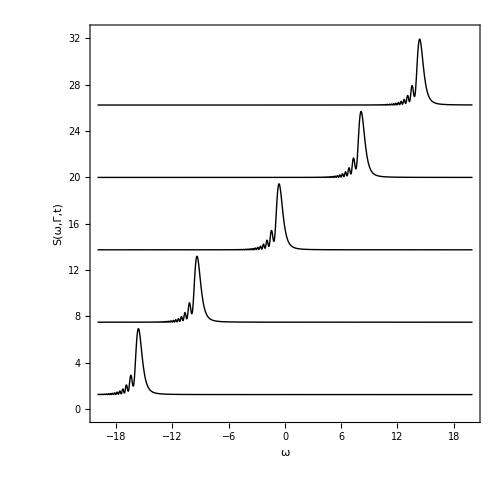

```mathematica
Show[P1, P2, P3, P4, P5]
```

## Dependencia de paso: Δ(t) = tan(βt/2) , Ω=0

```mathematica
H2 =MatrixForm[{{Tanh[(β^2) t / 2], Ω}, {Ω, -Tanh[(β^2) t / 2]}}]
```

(Tanh[(t β^2)/2] | Ω
Ω | -Tanh[(t β^2)/2])

```mathematica
Eigenvalues[%]
```

{-(√(-1+Ω^2+Cosh[t β^2]+Ω^2 Cosh[t β^2]))/(√(1+Cosh[t β^2])),(√(-1+Ω^2+Cosh[t β^2]+Ω^2 Cosh[t β^2]))/(√(1+Cosh[t β^2]))}

```mathematica
Eigenvectors[%]
```

Eigenvectors[{-(√(-1+Ω^2+Cosh[t β^2]+Ω^2 Cosh[t β^2]))/(√(1+Cosh[t β^2])),(√(-1+Ω^2+Cosh[t β^2]+Ω^2 Cosh[t β^2]))/(√(1+Cosh[t β^2]))}]

```mathematica
FullSimplify[%]
```

Eigenvectors[{-(√(-1+Ω^2+(1+Ω^2) Cosh[t β^2]))/(√(1+Cosh[t β^2])),(√(-1+Ω^2+(1+Ω^2) Cosh[t β^2]))/(√(1+Cosh[t β^2]))}]

```mathematica
Manipulate[Plot[{1Tanh[(β^2) t /2],-Tanh[(β^2) t /2],
(√(-1+Ω^2+(1+Ω^2) Cosh[t β^2]))/(√(1+Cosh[t β^2])),
-(√(-1+Ω^2+(1+Ω^2) Cosh[t β^2]))/(√(1+Cosh[t β^2]))},
{t,-61,61},
PlotRange->{-2.0,2.0},Frame->True,Axes->None,
FrameLabel->{Style["Time",25,FontFamily->"Times New Roman",Black],
Style["Energy",25,FontFamily->"Times New Roman",Black]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,
PlotStyle->{Directive[Green,Dashed,Thick],
Directive[Purple,Dashed,Thick],
Directive[Red,Thick],Directive[Blue,Thick]},
ImageSize->500,AspectRatio->1,
PlotLegends-> Placed[LineLegend[{Style["β=0.5",18,Black],None,Style["Ω=0.3", 18,Black]},
LegendFunction->(Framed[#,RoundingRadius->2,Background->White]&)],{0.18,0.89}]],
{{β,0.5},0.1,2},{{Ω,0.3},0.05,1}]
```

```mathematica
H2 =MatrixForm[{{Tanh[(β^2) t / 2], Ω}, {Ω, 0}}]
```

(Tanh[(t β^2)/2] | Ω
Ω | 0)

```mathematica
Eigenvalues[%]
```

{1/2 Sech[(t β^2)/2] ((√(-1+4 Ω^2+Cosh[t β^2]+4 Ω^2 Cosh[t β^2]))/(√2)+Sinh[(t β^2)/2]),1/2 (-(√(-1+4 Ω^2+Cosh[t β^2]+4 Ω^2 Cosh[t β^2]) Sech[(t β^2)/2])/(√2)+Tanh[(t β^2)/2])}

```mathematica
FullSimplify[%]
```

{1/4 (√(-2+8 Ω^2+(2+8 Ω^2) Cosh[t β^2]) Sech[(t β^2)/2]+2 Tanh[(t β^2)/2]),1/4 (-√(-2+8 Ω^2+(2+8 Ω^2) Cosh[t β^2]) Sech[(t β^2)/2]+2 Tanh[(t β^2)/2])}

```mathematica
Manipulate[Plot[{1Tanh[(β^2) t /2],0,
1/4 (√(-2+8 Ω^2+(2+8 Ω^2) Cosh[t β^2]) Sech[(t β^2)/2]+2 Tanh[(t β^2)/2]),
1/4 (-√(-2+8 Ω^2+(2+8 Ω^2) Cosh[t β^2]) Sech[(t β^2)/2]+2 Tanh[(t β^2)/2])},
{t,-61,61},
PlotRange->{-2.0,2.0},Frame->True,Axes->None,
FrameLabel->{Style["Time",25,FontFamily->"Times New Roman",Black],
Style["Energy",25,FontFamily->"Times New Roman",Black]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,
PlotStyle->{Directive[Green,Dashed,Thick],
Directive[Purple,Dashed,Thick],
Directive[Red,Thick],Directive[Blue,Thick]},
ImageSize->500,AspectRatio->1,
PlotLegends-> Placed[LineLegend[{Style["β=0.5",18,Black],None,Style["Ω=0.3", 18,Black]},
LegendFunction->(Framed[#,RoundingRadius->2,Background->White]&)],{0.18,0.89}]],
{{β,0.5},0.1,2},{{Ω,0.3},0.05,1}]
```

Analiticamente, llegamos a la siguiente expresión para el espectro fisico con esta variación temporal

```mathematica
Assuming[β>0&&Γ>0&&T>to&&Δ∈Reals,Integrate[Exp[(Γ -I Δ )t+I (2/β) Log[Cosh[β t/2]]],{t,to,T}]]
```

(ⅇ^(T (Γ-ⅈ Δ)) (1+ⅇ^(T β)) Cosh[(T β)/2]^(2 ⅈ/β) Hypergeometric2F1[1,(ⅈ+β+Γ-ⅈ Δ)/β,(β+Γ-ⅈ (1+Δ))/β,-ⅇ^(T β)]-ⅇ^(to (Γ-ⅈ Δ)) (1+ⅇ^(to β)) Cosh[(to β)/2]^(2 ⅈ/β) Hypergeometric2F1[1,(ⅈ+β+Γ-ⅈ Δ)/β,(β+Γ-ⅈ (1+Δ))/β,-ⅇ^(to β)])/(Γ-ⅈ (1+Δ))

```mathematica
Assuming[β>0&&Γ>0&&Δ∈Reals,Limit[ (1+ⅇ^(to β)) Hypergeometric2F1[1,(ⅈ+β+Γ-ⅈ Δ)/β,(β+Γ-ⅈ (1+Δ))/β,-ⅇ^(to β)],to->-Infinity]]
```

1

```mathematica
Assuming[β>0&&Γ>0&&Δ∈Reals,Limit[ⅇ^(to (Γ-ⅈ Δ)),to->-Infinity]]
```

0

```mathematica
Assuming[β>0&&Γ>0&&Δ∈Reals,Limit[ (1+ⅇ^(T β)) Hypergeometric2F1[1,(ⅈ+β+Γ-ⅈ Δ)/β,(β+Γ-ⅈ (1+Δ))/β,-ⅇ^(T β)],T->+Infinity]]
```

((Γ-ⅈ (1+Δ)) Gamma[(ⅈ+Γ-ⅈ Δ)/β])/(β Gamma[(ⅈ+β+Γ-ⅈ Δ)/β])

```mathematica
Assuming[β>0&&Γ>0&&Δ∈Reals,FullSimplify[Abs[Gamma[(ⅈ+Γ-ⅈ Δ)/β]/(β Gamma[(ⅈ+β+Γ-ⅈ Δ)/β])]^2]]
```

1/Abs[ⅈ+Γ-ⅈ Δ]^2

```mathematica
EW2TanhAnalitic[Γ_,β_,Δ_,T_]:=2Γ(Abs[(1+ⅇ^(T β)) Hypergeometric2F1[1,(ⅈ+β+Γ-ⅈ Δ)/β,(β+Γ-ⅈ (1+Δ))/β,-ⅇ^(T β)]]^2)/(Γ^2+ (Δ+1)^2)
```

```mathematica
P6 = ListPlot[ParallelTable[{Δ,80+EW2TanhAnalitic[0.1,(0.5),Δ,70.0]},{Δ,-2,2,0.01}],PlotRange->{-0.5,101.2},Filling->80,Joined->True,
Frame->True,PlotStyle->Directive[Black,Thickness[0.003]],
FrameLabel->{Style[ω,18],Style["S(ω,Γ,t)",18],Style["Γ=0.1,β=0.5,t=-70",18]},
FrameTicksStyle->18,Axes->None,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]],
ImageSize->500,AspectRatio->1]
```

```mathematica
P7 = ListPlot[ParallelTable[{Δ,60+EW2TanhAnalitic[0.1,(0.5),Δ,15.0]},{Δ,-2,2,0.01}],PlotRange->{-0.5,101.2},Filling->60,Joined->True,
Frame->True,PlotStyle->Directive[Black,Thickness[0.003]],
FrameLabel->{Style[ω,18],Style["S(ω,Γ,t)",18],Style["Γ=0.1,β=0.5,t=-70",18]},
FrameTicksStyle->18,Axes->None,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]],
ImageSize->500,AspectRatio->1]
```

```mathematica
P8 = ListPlot[ParallelTable[{Δ,40+EW2TanhAnalitic[0.1,(0.5),Δ,7.0]},{Δ,-2,2,0.01}],PlotRange->{-0.5,101.2},Filling->40,Joined->True,
Frame->True,PlotStyle->Directive[Black,Thickness[0.003]],
FrameLabel->{Style[ω,18],Style["S(ω,Γ,t)",18],Style["Γ=0.1,β=0.5,t=-70",18]},
FrameTicksStyle->18,Axes->None,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]],
ImageSize->500,AspectRatio->1]
```

```mathematica
P9 = ListPlot[ParallelTable[{Δ,20+EW2TanhAnalitic[0.1,(0.5),Δ,0.0]},{Δ,-2,2,0.01}],PlotRange->{-0.5,101.2},Filling->20,Joined->True,
Frame->True,PlotStyle->Directive[Black,Thickness[0.003]],
FrameLabel->{Style[ω,18],Style["S(ω,Γ,t)",18],Style["Γ=0.1,β=0.5,t=-70",18]},
FrameTicksStyle->18,Axes->None,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]],
ImageSize->500,AspectRatio->1]
```

```mathematica
P10 = ListPlot[ParallelTable[{Δ,0+EW2TanhAnalitic[0.1,(0.5),Δ,-10.0]},{Δ,-2,2,0.01}],PlotRange->{-0.5,101.2},Filling->0,Joined->True,
Frame->True,PlotStyle->Directive[Black,Thickness[0.003]],
FrameLabel->{Style[ω,18],Style["S(ω,Γ,t)",18],Style["Γ=0.1,β=0.5,t=-70",18]},
FrameTicksStyle->18,Axes->None,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]],
ImageSize->500,AspectRatio->1]
```

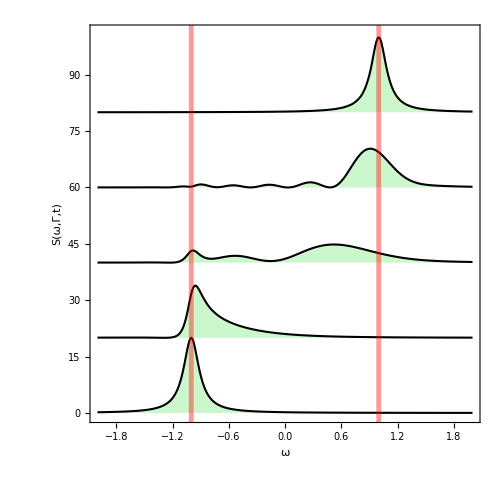

```mathematica
Show[P6, P7, P8, P9, P10, GridLines->{{{-1,Directive[Thickness[0.007],Red]},{+1,Directive[Thickness[0.007],Red]}},None}]
```

Por el contrario, podemos usar una solución númerica para la expresión del espectro EW

```mathematica
NumEW2Tanh[Γ_,β_,Δ_,to_,T_]:=2Γ Exp[-2 Γ T]*(Abs[NIntegrate[Exp[(Γ -I Δ )t+I (2/β) Log[Cosh[β t/2]]],{t,to,T}]]^2)
```

```mathematica
P6 = ListLinePlot[ParallelTable[{Δ,100+NumEW2Tanh[0.05,(0.5)^2,Δ,-200,70]},{Δ,-2,2,0.01}],PlotRange->{-0.5,140.2},Filling->100,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]],Joined->True,Frame->True,PlotStyle->Directive[Black,Thickness[0.003]],
FrameLabel->{Style[ω,18],Style["S(ω,Γ,t)",18],Style["Γ=0.1,β=0.5,t=-70",18]},
FrameTicksStyle->18, ImageSize->700,AspectRatio->0.7]
```

```mathematica
P7 = ListLinePlot[ParallelTable[{Δ,80+NumEW2Tanh[0.05,(0.5)^2,Δ,-200,20]},{Δ,-2,2,0.01}],PlotRange->{-0.5,140.2},Filling->80,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]],Joined->True,Frame->True,PlotStyle->Directive[Black,Thickness[0.003]],
FrameLabel->{Style[ω,18],Style["S(ω,Γ,t)",18],Style["Γ=0.1,β=0.5,t=-70",18]},
FrameTicksStyle->18, ImageSize->700,AspectRatio->0.7]
```

```mathematica
P8 = ListLinePlot[ParallelTable[{Δ,60+NumEW2Tanh[0.05,(0.5)^2,Δ,-200,5]},{Δ,-2,2,0.01}],PlotRange->{-0.5,140.2},Filling->60,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]],Joined->True,Frame->True,PlotStyle->Directive[Black,Thickness[0.003]],
FrameLabel->{Style[ω,18],Style["S(ω,Γ,t)",18],Style["Γ=0.1,β=0.5,t=-70",18]},
FrameTicksStyle->18, ImageSize->700,AspectRatio->0.7]
```

```mathematica
P9 = ListLinePlot[ParallelTable[{Δ,40+NumEW2Tanh[0.05,(0.5)^2,Δ,-200,0]},{Δ,-2,2,0.01}],PlotRange->{-0.5,140.2},Filling->40,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]],Joined->True,Frame->True,PlotStyle->Directive[Black,Thickness[0.003]],
FrameLabel->{Style[ω,18],Style["S(ω,Γ,t)",18],Style["Γ=0.1,β=0.5,t=-70",18]},
FrameTicksStyle->18, ImageSize->700,AspectRatio->0.7]
```

```mathematica
P10 = ListLinePlot[ParallelTable[{Δ,0+NumEW2Tanh[0.05,(0.5)^2,Δ,-200,-10]},{Δ,-2,2,0.01}],PlotRange->{-0.5,140.2},Filling->0,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]],Joined->True,Frame->True,PlotStyle->Directive[Black,Thickness[0.003]],
FrameLabel->{Style[ω,18],Style["S(ω,Γ,t)",18],Style["Γ=0.1,β=0.5,t=-70",18]},
FrameTicksStyle->18, ImageSize->700,AspectRatio->0.7]
```

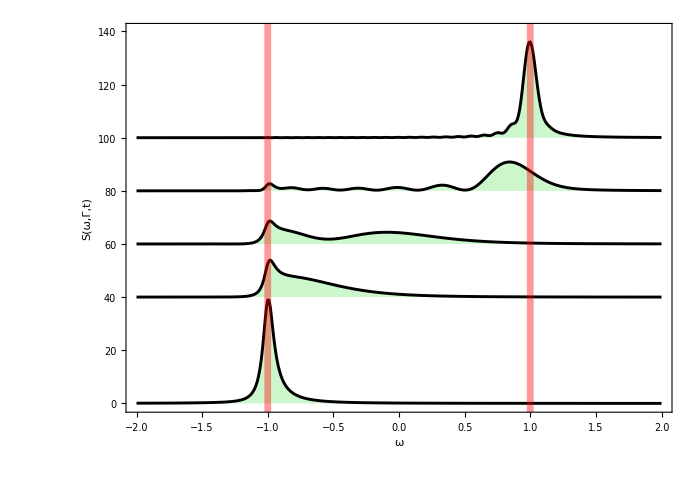

```mathematica
Show[P6, P7, P8, P9, P10, GridLines->{{{-1,Directive[Thickness[0.007],Red]},{+1,Directive[Thickness[0.007],Red]}},None}]
```

## Dependencia Periodica Δ(t) = cos(ν t) , Ω=0

```mathematica
H3 = MatrixForm[{{A Cos[ν t], Ω}, {Ω, - A Cos[ν t]}}]
```

(A Cos[t ν] | Ω
Ω | -A Cos[t ν])

```mathematica
Eigenvalues[%]
```

{-(√(A^2+2 Ω^2+A^2 Cos[2 t ν]))/(√2),(√(A^2+2 Ω^2+A^2 Cos[2 t ν]))/(√2)}

```mathematica
FullSimplify[%]
```

{-(√(A^2+2 Ω^2+A^2 Cos[2 t ν]))/(√2),(√(A^2+2 Ω^2+A^2 Cos[2 t ν]))/(√2)}

```mathematica
Manipulate[Plot[{A Cos[t ν],- A Cos[t ν],
(√(A^2+2 Ω^2+A^2 Cos[2 t ν]))/(√2),
-(√(A^2+2 Ω^2+A^2 Cos[2 t ν]))/(√2)},{t,-80.1,80.1},
PlotRange->{-1.5,1.5},Frame->True,Axes->None,
FrameLabel->{Style["Time",25,FontFamily->"Times New Roman",Black],
Style["Energy",25,FontFamily->"Times New Roman",Black]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,
PlotStyle->{Directive[Green,Dashed,Thick],
Directive[Purple,Dashed,Thick],
Directive[Red,Thick],Directive[Blue,Thick]},
ImageSize->500,AspectRatio->1,
PlotLegends-> Placed[LineLegend[{Style["ν=0.04",18,Black],None,Style["Ω=0.2", 18,Black]},
LegendFunction->(Framed[#,RoundingRadius->2,Background->White]&)],{0.18,0.88}]]
,{{A,1},0.1,6},{{ν,0.04},0.01,0.2},{{Ω,0.2},0.05,2}]
```

```mathematica
H3 = MatrixForm[{{A Cos[ν t], Ω}, {Ω, 0}}]
```

(A Cos[t ν] | Ω
Ω | 0)

```mathematica
Eigenvalues[%]
```

{1/2 (A Cos[t ν]-√(4 Ω^2+A^2 Cos[t ν]^2)),1/2 (A Cos[t ν]+√(4 Ω^2+A^2 Cos[t ν]^2))}

```mathematica
FullSimplify[%]
```

{1/2 (A Cos[t ν]-√(4 Ω^2+A^2 Cos[t ν]^2)),1/2 (A Cos[t ν]+√(4 Ω^2+A^2 Cos[t ν]^2))}

```mathematica
Manipulate[Plot[{A Cos[t ν],0,
1/2 (A Cos[t ν]-√(4 Ω^2+A^2 Cos[t ν]^2)),
1/2 (A Cos[t ν]+√(4 Ω^2+A^2 Cos[t ν]^2))},{t,-80.1,80.1},
PlotRange->{-1.5,1.5},Frame->True,Axes->None,
FrameLabel->{Style["Time",25,FontFamily->"Times New Roman",Black],
Style["Energy",25,FontFamily->"Times New Roman",Black]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,
PlotStyle->{Directive[Green,Dashed,Thick],
Directive[Purple,Dashed,Thick],
Directive[Red,Thick],Directive[Blue,Thick]},
ImageSize->500,AspectRatio->1,
PlotLegends-> Placed[LineLegend[{Style["ν=0.04",18,Black],None,Style["Ω=0.2", 18,Black]},
LegendFunction->(Framed[#,RoundingRadius->2,Background->White]&)],{0.18,0.88}]]
,{{A,1},0.1,6},{{ν,0.04},0.01,0.2},{{Ω,0.2},0.05,2}]
```

Llegamos a una expresión analitica para el espectro EW en la que debemos resolver la siguiente integral de forma analitica

```mathematica
NumEW3Periodic[Γ_,ν_,Δ_,to_,T_]:=2Γ Exp[-2 Γ T]*(Abs[NIntegrate[Exp[(Γ -I Δ )t+I (1/ν) Sin[ν t]],{t,to,T}]]^2)
```

```mathematica
P11 = ListPlot[ParallelTable[{ω,120+NumEW3Periodic[0.1,(0.2)^2,ω,-150,95]},{ω,-2,2,0.05}],PlotRange->{-0.5,140.2},Filling->120,FrameTicksStyle->18,Joined->True,
Frame->True,PlotStyle->Directive[Black,Thickness[0.003]],
FrameLabel->{Style[ω,18],Style["S(ω,Γ,t)",18],Style["Γ=0.1,β=0.5,t=-70",18]},Axes->None,
FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]],
InterpolationOrder->2,ImageSize->500,AspectRatio->1]
```

```mathematica
P12 = ListPlot[ParallelTable[{ω,100+NumEW3Periodic[0.1,(0.2)^2,ω,-150,65]},{ω,-2,2,0.05}],PlotRange->{-0.5,140.2},Filling->100,FrameTicksStyle->18{
NDSolveValue[{x'[t]-2 x[t] y'[t]==-ⅈ Ω (1+x[t]^2),y'[t]==ⅈ (-t β^2+Ω x[t]),True,x[0]==y[0]==z[0]==0},{x,y,z},{t,20}],Joined->True,
Frame->True,PlotStyle->Directive[Black,Thickness[0.003]],
FrameLabel->{Style[ω,18],Style["S(ω,Γ,t)",18],Style["Γ=0.1,β=0.5,t=-70",18]},Axes->None,
FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]],
InterpolationOrder->2,ImageSize->500,AspectRatio->1]
```

```mathematica
P13 = ListPlot[ParallelTable[{ω,80+NumEW3Periodic[0.1,(0.2)^2,ω,-150,35]},{ω,-2,2,0.05}],PlotRange->{-0.5,140.2},Filling->80,FrameTicksStyle->18,Joined->True,
Frame->True,PlotStyle->Directive[Black,Thickness[0.003]],
FrameLabel->{Style[ω,18],Style["S(ω,Γ,t)",18],Style["Γ=0.1,β=0.5,t=-70",18]},Axes->None,
FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]],
InterpolationOrder->2,ImageSize->500,AspectRatio->1]
```

```mathematica
P14 = ListPlot[ParallelTable[{ω,60+NumEW3Periodic[0.1,(0.2)^2,ω,-150,0]},{ω,-2,2,0.05}],PlotRange->{-0.5,140.2},Filling->60,FrameTicksStyle->18,Joined->True,
Frame->True,PlotStyle->Directive[Black,Thickness[0.003]],
FrameLabel->{Style[ω,18],Style["S(ω,Γ,t)",18],Style["Γ=0.1,β=0.5,t=-70",18]},Axes->None,
FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]],
InterpolationOrder->2,ImageSize->500,AspectRatio->1]
```

```mathematica
P15 = ListPlot[ParallelTable[{ω,40+NumEW3Periodic[0.1,(0.2)^2,ω,-150,-35]},{ω,-2,2,0.05}],PlotRange->{-0.5,140.2},Filling->40,FrameTicksStyle->18,Joined->True,
Frame->True,PlotStyle->Directive[Black,Thickness[0.003]],
FrameLabel->{Style[ω,18],Style["S(ω,Γ,t)",18],Style["Γ=0.1,β=0.5,t=-70",18]},Axes->None,
FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]],
InterpolationOrder->2,ImageSize->500,AspectRatio->1]
```

```mathematica
P16 = ListPlot[ParallelTable[{ω,20+NumEW3Periodic[0.1,(0.2)^2,ω,-150,-65]},{ω,-2,2,0.05}],PlotRange->{-0.5,140.2},Filling->20,FrameTicksStyle->18,Joined->True,
Frame->True,PlotStyle->Directive[Black,Thickness[0.003]],
FrameLabel->{Style[ω,18],Style["S(ω,Γ,t)",18],Style["Γ=0.1,β=0.5,t=-70",18]},Axes->None,
FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]],
InterpolationOrder->2,ImageSize->500,AspectRatio->1]
```

```mathematica
P17 = ListPlot[ParallelTable[{ω,0+NumEW3Periodic[0.1,(0.2)^2,ω,-150,-95]},{ω,-2,2,0.05}],PlotRange->{-0.5,140.2},Filling->0,FrameTicksStyle->18,Joined->True,
Frame->True,PlotStyle->Directive[Black,Thickness[0.003]],
FrameLabel->{Style[ω,18],Style["S(ω,Γ,t)",18],Style["Γ=0.1,β=0.5,t=-70",18]},Axes->None,
FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]],
InterpolationOrder->2,ImageSize->500,AspectRatio->1]
```

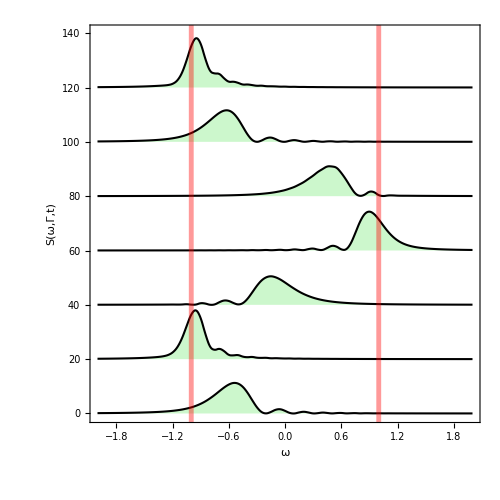

```mathematica
Show[P11, P12, P13, P14, P15, P16, P17, GridLines->{{{-1,Directive[Thickness[0.007],Red]},{+1,Directive[Thickness[0.007],Red]}},None}]
```

## Landau-Zener

Solución analitica para la ecuación de α_+

```mathematica
DSolveValue[{y'[t]- I Ω y[t]^2 + 2 I (β^2)t y[t] + I  Ω==0,y[0]==0},y[t],t]
```

(2 t β^2 Hypergeometric1F1[-(-2 β^2-ⅈ Ω^2)/(4 β^2),1/2,ⅈ t^2 β^2]-2 t β^2 Hypergeometric1F1[1-(-2 β^2-ⅈ Ω^2)/(4 β^2),3/2,ⅈ t^2 β^2]-ⅈ t Ω^2 Hypergeometric1F1[1-(-2 β^2-ⅈ Ω^2)/(4 β^2),3/2,ⅈ t^2 β^2])/(Ω Hypergeometric1F1[-(-2 β^2-ⅈ Ω^2)/(4 β^2),1/2,ⅈ t^2 β^2])